# Homework 6

## Mario Hernandez & Alec Ramos

## Part 1

### uCatchMeVersion1

```mathematica
oneRunnerStep1[runnerCo_,catcherCo_,runnerSpeed_,rad_,timestep_]:=

N[{runnerCo[[1]]+((runnerCo[[1]]-catcherCo[[1]])(runnerSpeed*timestep))/EuclideanDistance[runnerCo,catcherCo],
runnerCo[[2]]+((runnerCo[[2]]-catcherCo[[2]])(runnerSpeed*timestep))/EuclideanDistance[runnerCo,catcherCo]}]
```

```mathematica
oneCatcherStep[runnerCo_,catcherCo_,catcherSpeed_,timestep_]:=

N[{catcherCo[[1]]+((runnerCo[[1]]-catcherCo[[1]])(catcherSpeed*timestep))/EuclideanDistance[runnerCo,catcherCo],
catcherCo[[2]]+((runnerCo[[2]]-catcherCo[[2]])(catcherSpeed*timestep))/EuclideanDistance[runnerCo,catcherCo]}]
```

```mathematica
multipleSteps1[runnerCo_,runnerSpeed_,catcherCo_,catcherSpeed_,rad_,timeStep_,stepNumb_]:=Module[
{i,catcherLine ={catcherCo},runnerLine={runnerCo},currCat=catcherCo,currRun=runnerCo},
For[i=1,i≤stepNumb,i++,
If[EuclideanDistance[currCat,currRun]<(timeStep*catcherSpeed)||RegionDistance[Circle[{0,0}, rad], currRun]<timeStep*runnerSpeed,
Break[]
];
AppendTo[catcherLine,oneCatcherStep[currRun,currCat,catcherSpeed,timeStep]];
AppendTo[runnerLine,oneRunnerStep1[currRun,currCat,runnerSpeed,rad,timeStep]];
currCat=Last[catcherLine];
currRun=Last[runnerLine];
];
Return[{catcherLine,runnerLine}];
]
```

```mathematica
(*moves a runner and catcher in a line towards a boundary until runner is caught or runner is close enough to the boundary*)
uCatcher1[runnerCo_, runnerSpeed_, catcherCo_, catcherSpeed_, radius_, timeStep_, stepNumb_]:=
Show[{
Graphics[Circle[{0,0},radius]],
Graphics[Style[Line[{runnerCo,runnerCo}],Red,Thickness[radius/200]]],
Graphics[Style[Line[{catcherCo,catcherCo}],Blue,Thickness[radius/200]]],
Graphics[Style[Line[multipleSteps1[runnerCo,runnerSpeed,catcherCo,catcherSpeed,radius,timeStep,stepNumb][[1]]],Blue]],
Graphics[Style[Line[multipleSteps1[runnerCo,runnerSpeed,catcherCo,catcherSpeed,radius,timeStep,stepNumb][[2]]],Red]]
}]
```

```mathematica
Manipulate[uCatcher1[{0,0},2,{1,0},1,5,1,u],{{u,0,"Steps"}, 0, 20}]
```

## Part 2

### uCatchMeVersion2

```mathematica
(*runner must be close to edge*)
oneRunnerStep2[runnerCo_, catcherCo_, runnerSpeed_, rad_, timeStep_]:=Module[{resultSet},
resultSet={newx, newy}/.NSolve[{newx^2+newy^2==rad^2,(newx-runnerCo[[1]])^2+(newy-runnerCo[[2]])^2==(runnerSpeed*timeStep)^2}, {newx, newy}];
If[EuclideanDistance[catcherCo, resultSet[[1]]]≥EuclideanDistance[catcherCo, resultSet[[2]]],
resultSet[[1]],
resultSet[[2]]
]
]
```

```mathematica
oneRunnerStep[{3,2}, {-2,0}, 1,5,2]
```

{4.84615,1.23077}

```mathematica
multipleSteps2[runnerCo_,runnerSpeed_,catcherCo_,catcherSpeed_,rad_,timeStep_,stepNumb_]:=Module[
{step,catcherLine ={catcherCo},runnerLine={runnerCo},currCat=catcherCo,currRun=runnerCo},
For[step=1,step≤stepNumb,step++,
If[EuclideanDistance[currCat,currRun]<(timeStep*catcherSpeed),
Break[]
];
AppendTo[catcherLine,oneCatcherStep[currRun,currCat,catcherSpeed,timeStep]];
AppendTo[runnerLine,oneRunnerStep2[currRun,currCat,runnerSpeed,rad,timeStep]];
currCat=Last[catcherLine];
currRun=Last[runnerLine];
];
Return[{catcherLine,runnerLine}];
]
```

```mathematica
multipleSteps1[{0,2},1,{1,0},1,5,2,7]
```

{{{1,0},{0.105573,1.78885}},{{0,2},{-0.894427,3.78885}}}

```mathematica
uCatcher2[runnerCo_,catcherCo_,catcherSpeed_,runnerSpeed_,timestep_,numStep_,radius_]:=
Show[{
Graphics[Circle[{0,0},radius]],
Graphics[Style[Line[{runnerCo,runnerCo}],Red,Thickness[radius/200]]],
Graphics[Style[Line[{catcherCo,catcherCo}],Blue,Thickness[radius/200]]],
Graphics[
{Style[Line[multipleSteps2[runnerCo,runnerSpeed,catcherCo,catcherSpeed,radius,timestep,numStep][[1]]],Blue],Style[Line[multipleSteps2[runnerCo,runnerSpeed,catcherCo,catcherSpeed,radius,timestep,numStep][[2]]],Red]}]
}]
```

```mathematica
Manipulate[uCatcher2[{0,5},{1,0},2,2,1,u,5],{{u,0,"Steps"}, 0, 10}]
```

## Part 3

### uCatcher3

```mathematica
multipleSteps3[runnerCo_,  runnerSpeed_, catcherCo_, catcherSpeed_, rad_, timeStep_, stepNumb_]:=Module[
{runnerList={},catcherList={},stepList={},stepsLeft,stepList2,item},

stepList=multipleSteps1[runnerCo,runnerSpeed,catcherCo,catcherSpeed,rad,timeStep,stepNumb];

runnerList=stepList[[2]];
catcherList=stepList[[1]];

stepsLeft=stepNumb-Length[runnerList];

stepList2=multipleSteps2[Last[runnerList],runnerSpeed,Last[catcherList],catcherSpeed,rad,timeStep,stepsLeft];

For[item=1,item<Length[stepList2[[2]]],item++,
AppendTo[runnerList,stepList2[[2,item]]];
];
For[item=1,item<Length[stepList2[[1]]],item++,
AppendTo[catcherList,stepList2[[1,item]]];
];

runnerList=DeleteDuplicates[runnerList];
catcherList=DeleteDuplicates[catcherList];

{catcherList,runnerList}
]
```

```mathematica
jeff=multipleSteps3[{0,2},1,{1,0},1,5,1,10]
```

{{0,2},{-0.447214,2.89443},{-0.894427,3.78885},{-1.34164,4.68328},{-1.34164,4.68328},{-2.31015,4.43432},{-3.14637,3.88592},{-3.85673,3.18208},{-4.41282,2.35096},{-4.7924,1.4258}}

{{{1,0},{0.552786,0.894427},{0.105573,1.78885},{-0.341641,2.68328},{-0.788854,3.57771},{-1.66021,4.06835},{-2.65276,3.94651},{-3.49697,3.4105},{-4.15092,2.65395}},{{0,2},{-0.447214,2.89443},{-0.894427,3.78885},{-1.34164,4.68328},{-2.31015,4.43432},{-3.14637,3.88592},{-3.85673,3.18208},{-4.41282,2.35096},{-4.7924,1.4258}}}

```mathematica
uCatcher3[runnerCo_,catcherCo_,catcherSpeed_,runnerSpeed_,timestep_,numStep_,radius_]:=
Show[
Graphics[{
Circle[{0,0},radius],
{Red,PointSize[Large], Point[runnerCo]},
{Blue,PointSize[Large],Point[catcherCo]},
{Style[Line[multipleSteps3[runnerCo,runnerSpeed,catcherCo,catcherSpeed,radius,timestep,numStep][[1]]],Blue,Thick],Style[Line[multipleSteps3[runnerCo,runnerSpeed,catcherCo,catcherSpeed,radius,timestep,numStep][[2]]],Red,Thick,Dashed]}
}]
]
```

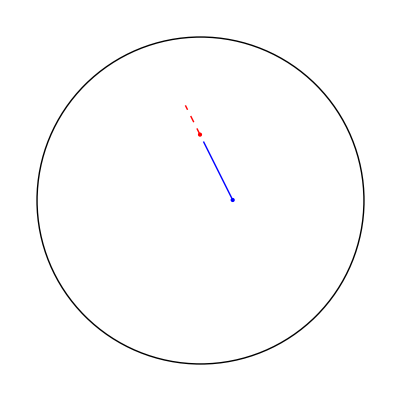

```mathematica
uCatcher3[{0,2},{1,0},2,1,1,3,5]
```

```mathematica
(*uCatcher3[runnerCo_,catcherCo_,catcherSpeed_,runnerSpeed_,timestep_,numStep_,radius_]*)
```

```mathematica
Manipulate[uCatcher3[{0,2},{1,0},2,1,1,u,5],{{u,0,"Steps"},0,10}]
```

## Part 4

### i

1) if catcher is double speed than runner then it will catch in rad/ctcher speed floor

```mathematica
Manipulate[uCatcher3[{1,2},{-2,1},3,1.5,1,u,5],{{u,0,"Steps"},0,10}]
```

2)when timestep is greater than the distance between the catcher and runner the runner will be caught in 1 step

```mathematica
Manipulate[uCatcher3[{1,0},{0,1},1,1,2,u,5],{{u,0,"Steps"},0,10}]
```

```mathematica
EuclideanDistance[{1,0},{0,1}]
```

√2

```mathematica
2>√2
```

True

```mathematica
Manipulate[uCatcher3[{1,1},{0,1},1,1,2,u,5],{{u,0,"Steps"},0,10}]
```

```mathematica
2>EuclideanDistance[{1,1},{0,1}]
```

True

3) runner fast catcher not

4)the distance between the runner and the catcher is greater than the time step *catchers peed

### ii

5) runner could change direction from the catcher to try to increase distance between them

## Part 5

### i

Both catchers run towards where the runner would be in one step. Also, the catchers want to be some distance away from each other to maximize the chance that they catch the runner.

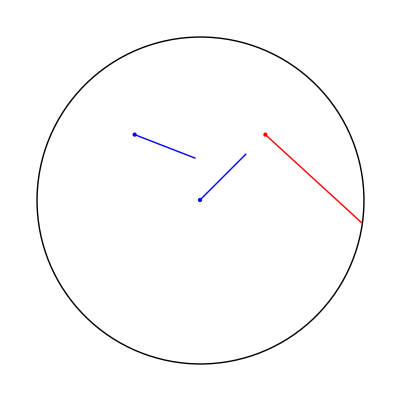

```mathematica
uCatcherMeVersion4[{2,2},2,{0, 0}, {-2,2 }, 1,5,2,3]
```

In the picture above, the catcher on the left is currently going towards the current position of the runner, not the position from a previous step.

#### ii

If the catchers employ the strategy from part i, the runner could go to the boundary and go in a circle. Depending on the initial position of the catchers, the runner will go a long time without being caught. Also, increasing the runner speed would make catching it nearly impossible.

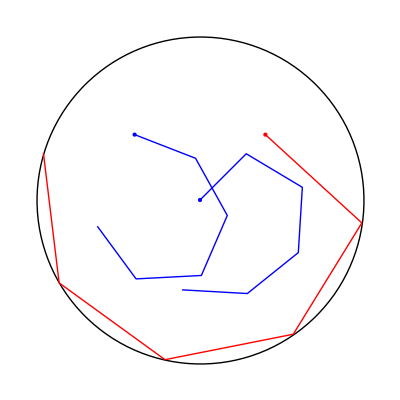

```mathematica
uCatcherMeVersion4[{2,2},2,{0, 0}, {-2,2 }, 1,5,2,7]
```

In the above picture, the runner goes to the boundary with a greater speed than the runners, and it travels around the circle.

#### iii

The distance between the catchers can just be passed in to be something relatively large.

Both catchers take in the runnerCo of the runners current coordinates after oneStepRunner.

#### iv

```mathematica
oneCatcherStep[runnerCo_,catcherCo_,catcherSpeed_,timestep_]:=

N[{catcherCo[[1]]+((runnerCo[[1]]-catcherCo[[1]])(catcherSpeed*timestep))/EuclideanDistance[runnerCo,catcherCo],
catcherCo[[2]]+((runnerCo[[2]]-catcherCo[[2]])(catcherSpeed*timestep))/EuclideanDistance[runnerCo,catcherCo]}]
```

```mathematica
multipleSteps4[runnerCo_, runnerSpeed_, catcherCo1_, catcherCo2_, catcherSpeed_, rad_, timeStep_, stepNumb_]:=
Module[
{runnerList,catcherList1,catcherList2,stepList1,stepList2,stepsLeft,stepListNext1, stepListNext2,item, newRunner},

(*stepList 1 is the steps taken by the first catchers when both it and the runner are still moving in a straight line*)
(*stepList 2 just chases the runner using the runner's current position at this stage*)
stepList1=multipleSteps1[runnerCo,runnerSpeed,catcherCo1,catcherSpeed,rad,timeStep,stepNumb];
stepList2=multipleSteps1[runnerCo, runnerSpeed, catcherCo2, catcherSpeed, rad, timeStep, stepNumb];

(*the runner reacts to the first catcher*)
runnerList=stepList1[[2]];
catcherList1=stepList1[[1]];
catcherList2=stepList2[[1]];

(*maintains the number of steps allowed*)
stepsLeft=stepNumb-Length[runnerList];

newRunner =oneRunnerStep2[Last[runnerList],Last[catcherList1],runnerSpeed, rad, timeStep];

(*next 2 lists give the new steps that involve the runner and catchers moving in a nonlinear way. We believe that the bug is here because the second catcher can use the updated runner position in the code. However, uncommenting the code in the next line to replace Last[runnerList] will be make the runner perform too many steps.*)
stepListNext1=multipleSteps2[(*oneRunnerStep2[Last[runnerList],Last[catcherList1],runnerSpeed, rad, timeStep]*)Last[runnerList],runnerSpeed,Last[catcherList1],catcherSpeed,rad,timeStep,stepsLeft];
stepListNext2=multipleSteps2[oneRunnerStep2[Last[runnerList],Last[catcherList1],runnerSpeed, rad, timeStep],runnerSpeed, Last[catcherList2], catcherSpeed, rad, timeStep, stepsLeft];


(* appends each new element to respective role's current list *)
For[item=1,item<Length[stepListNext1[[2]]],item++,
AppendTo[runnerList,stepListNext1[[2,item]]]
];
For[item=1,item<Length[stepListNext1[[1]]],item++,
AppendTo[catcherList1,stepListNext1[[1,item]]]
];
For[item=1,item<Length[stepListNext2[[1]]],item++,
AppendTo[catcherList2, stepListNext2[[1,item]]]
];

(* deletes duplicate between multipleSteps1 and multipleSteps2*)
runnerList=DeleteDuplicates[runnerList];
catcherList1=DeleteDuplicates[catcherList1];
catcherList2=DeleteDuplicates[catcherList2];

{runnerList,catcherList1, catcherList2}
]
```

```mathematica
uCatcherMeVersion4[runnerCo_, runnerSpeed_, catcherCo1_, catcherCo2_, catcherSpeed_, rad_,timeStep_, stepNumb_]:= 
Show[
Graphics[{
Circle[{0,0},rad],
{Red, PointSize[Large],Point[runnerCo]},
{Blue,PointSize[Large],Point[{catcherCo1,catcherCo2}]},
{Style[Line[multipleSteps4[runnerCo,runnerSpeed,catcherCo1,catcherCo2,catcherSpeed,rad,timeStep,stepNumb][[1]]],Red,Thick],Style[Line[multipleSteps4[runnerCo,runnerSpeed,catcherCo1,catcherCo2,catcherSpeed,rad,timeStep,stepNumb][[2]]],Blue,Thick],
Style[Line[multipleSteps4[runnerCo,runnerSpeed,catcherCo1,catcherCo2,catcherSpeed,rad,timeStep,stepNumb][[3]]],Blue,Thick]}
}
]
]
```

```mathematica
uCatcherMeVersion4[{2,2},2,{0, 0}, {-2,2 }, 1,5,2,7]
```

-Graphics-

```mathematica
Manipulate[uCatcherMeVersion4[{2,2},2, {0,0}, {-2,2}, 1, 5,2,u], {{u, 0,"Steps"},0,17}]
```

stepNumb is reached. Used for testing, shows that a much larger runner speed makes catching difficult.

```mathematica
Manipulate[uCatcherMeVersion4[{0,3},1, {-3,1}, {1,1}, 1, 5,2,u], {{u, 0,"Steps"},0,17}]
```

Runner is caught. Catcher 2 predicts the runner.

```mathematica
Manipulate[uCatcherMeVersion4[{0, 0},1.5, {3,0}, {-3,0}, 1, 5,2,u], {{u, 0,"Steps"},0,17}]
```

Runner is caught. Distance between catchers is large (greater than the radius).

```mathematica
Manipulate[uCatcherMeVersion4[{0,3},1, {-3,1}, {3, 0}, .5, 5,1,u], {{u, 0,"Steps"},0,17}]
```

stepNumb is reached. Catchers start apart. A bug is evident by catcher 2 going in a curve away from the runner. Found to occur sometimes when the runner starts somewhere “between” (see above for example) the catchers.

```mathematica
Manipulate[uCatcherMeVersion4[{4,3},.75, {-4,3}, {2,2}, .5, 5,2,u], {{u, 0,"Steps"},0,17}]
```

stepNumb is reached. Catcher speed is not much less than runner speed, and catcher 2 starts fairly close to the runner, yet they couldn’t catch it.